## Definitions

```mathematica
totalspin[]:=Total[Ising,Infinity]
pbc[z_]:=Module[{z0=z},If[z0>size,z0=z0-size];If[z0<1,z0=z0+size];z0]
pointenergy[sx_,sy_]:=(-1/2)*J*(Ising[[pbc[sx]]][[pbc[sy]]]*Ising[[pbc[sx+1]]][[pbc[sy]]]+Ising[[pbc[sx]]][[pbc[sy]]]*Ising[[pbc[sx]]][[pbc[sy+1]]]+Ising[[pbc[sx]]][[pbc[sy]]]*Ising[[pbc[sx-1]]][[pbc[sy]]]+Ising[[pbc[sx]]][[pbc[sy]]]*Ising[[pbc[sx]]][[pbc[sy-1]]])
totalenergy[]:=Module[{q=0},For[i=1,i≤size,i++,For[j=1,j≤size,j++,q=q+pointenergy[i,j]]];q]
flip[]:=Module[{x=RandomInteger[{1,size}],y=RandomInteger[{1,size}],ebefore,ediff,sbefore,sdiff,boltz},ebefore=pointenergy[x,y]+pointenergy[x+1,y]+pointenergy[x,y+1]+pointenergy[x-1,y]+pointenergy[x,y-1];sbefore=Ising[[x]][[y]];Ising[[x]][[y]]=Ising[[x]][[y]]*-1;ediff=ebefore-(pointenergy[x,y]+pointenergy[x+1,y]+pointenergy[x,y+1]+pointenergy[x-1,y]+pointenergy[x,y-1]);boltz=Exp[ediff/temperature];sdiff=sbefore-Ising[[x]][[y]];If[boltz>1,{energy=energy-ediff,spin=spin-sdiff},If[RandomReal[]<boltz,{energy=energy-ediff,spin=spin-sdiff},Ising[[x]][[y]]=Ising[[x]][[y]]*-1]]]
```

## Initialization

```mathematica
size=10;Ising=RandomInteger[{0,1},{size,size}]//(#*2-1)&;
(*Ising=ConstantArray[1,{size,size}];*)
Dynamic[ArrayPlot[Ising,PlotRange->{-1,1},Mesh->True]]
spin=totalspin[];
energy=totalenergy[];
Dynamic[{flipnum,temperature,spin,energy}]
```

## Simulation

```mathematica
temperature=4.5;
J=1;
movenum=5*10^4;
deltaT=temperature/movenum;
flipnum=0;
flushnum=Min[10^4,movenum/100];
keepnum=movenum/flushnum;
flushlist={};
keeplist={};
flipaction:=Module[{},flip[];flipnum++;temperature=N[temperature-deltaT];AppendTo[flushlist,{temperature,spin,energy,energy^2}]]
flushaction:=Module[{},If[Mod[flipnum,flushnum]==0,AppendTo[keeplist,Mean[flushlist]];flushlist={};ClearSystemCache[]]]
Do[flipaction[];flushaction[],movenum];
Print[keepnum,Dimensions[keeplist]]
```

100{100,4}

## Analysis

```mathematica
T=Transpose[keeplist];
tlist=T[[1]];
slist=T[[2]];
elist=T[[3]];
elist2=T[[4]];
hlist=(elist2-elist^2)/tlist^2;
Tc=2.269;
```

```mathematica
(*P1.11 part b*)
(*graph for size=100 and movenum=5x10^5 starting at temperature=4.5*)
-Graphics-
```

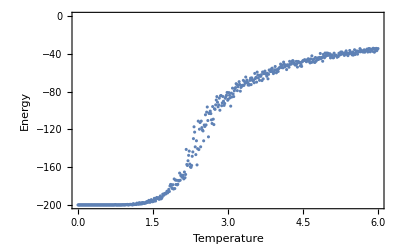

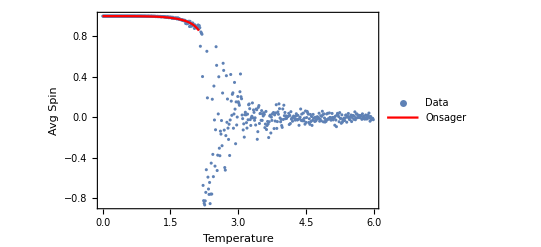

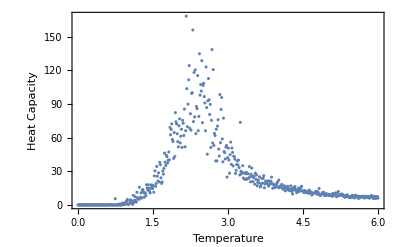

```mathematica
(*P1.11 part c*)
(*for size=10 and movenum=5x10^6 with starting temperature=6*)
(*this is the code used to generate the graphs below*)
ListPlot[Transpose[{tlist,elist}],{PlotRange->All,BaseStyle->{FontSize->18},AxesOrigin->{2.269,0},Frame->True,FrameLabel->{"Temperature","Energy"}}]
Show[ListPlot[Transpose[{tlist,(slist/(size*size))}],{PlotRange->All,BaseStyle->{FontSize->18},AxesOrigin->{2.269,0},Frame->True,FrameLabel->{"Temperature","Avg Spin"},PlotLegends->LineLegend[{"Data"}]}],Plot[(1-(Sinh[Log[(1+Sqrt[2])*(Tc/t)]])^-4)^(1/8),{t,0,Tc},PlotStyle->Red,PlotLegends->LineLegend[{"Onsager"}]]]
ListPlot[Transpose[{tlist,hlist}],{PlotRange->All,BaseStyle->{FontSize->18},AxesOrigin->{2.269,0},Frame->True,FrameLabel->{"Temperature","Heat Capacity"}}]
```

```mathematica
(*P1.11 part d*)
(*The observed transition temperature seems to be a little higher than the exact value given by Onsager. This can be seen in the heat capacity graph above where the peak happens just a little bit further up from where the line is that marks Onsager's exact solution. According to P1.9, this may be due to the finite size of our model, where Onsager's solution is exact for infinite models. The mean field theory predicts a temperature that is almost twice the size of Onsager (4/2.269 = 1.76), so would also be quite a bit larger than our observed transition temp*)
(*P1.11 part e*)
(*The spin fluctuates this way because as the temperature approaches the critical temperature from above, the correlation length (average size of "island" of spins) diverges with a power law dependence. The average spin, as seen in my graph above, fluctuates around zero for temperatures well above Tc, but ultimately grow in size and diverges as a power law dependence too. Its not until after passing Tc that the fluctuations become stable and tend towards their limiting values. As for the energy, it depends on the correlation length, which grows before we reach Tc, which causes the total energy to decrease. Then, below the transition we see the formation of a single domain as spontaneous magnetization kicks in, and the energy moves towards global minimum.*)
(*P1.11 part f*)
(*I watched the crital-opalescence of C02. I noticed that when passing through a boundary, the physical boundary between the liquid C02 and gas vanished, and they essentially became one. Also, as the fluid approaches the critical point, it becomes opaque, which apparently is from the critical density fluctuations diverging and becoming large enough to scatter light.*)
```